```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"AnSEL.m"]
```

# AnSEL - Analysis and Simplification of Equations with Loops

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[AnSEL]=True;
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

```mathematica
ClearAll[followLoop,GetLoops,i];
followLoop[setup_,term_FTerm,openIndices_,closedIndices_,allObj_,start_,startIdx_,oldmemory_:{}]:=Module[
{memory=oldmemory,curPos=start,curIdx=startIdx,curIndices,nextIdx,continue=True},
i=1;
While[i<9,
curIndices=makePosIdx/@curPos[[2]];
nextIdx=Select[curIndices,(#=!=curIdx&&FreeQ[openIndices,#])&];
(*Print["cur is ",curIdx," and ",nextIdx];*)
If[Length[memory]>0&&curPos===memory[[1]],Print[oi];Break[]];
If[Length[nextIdx]===1||Length[memory]===0,
AppendTo[memory,curPos];
curPos=Select[allObj,(MemberQ[#[[2]],nextIdx[[1]],{1,4}]&&#=!=curPos)&][[1]];
curIdx=nextIdx[[1]];
(*Print[curPos];*)
];
i++;
];
Return[memory];
];

GetLoops[setup_,expr_FTerm]:=Module[
{doFields,term,
openIndices,closedIndices,allObj,firsts,i},
doFields=Thread[(#[a__]&/@GetAllFields[setup])->(Field[{#},{a}]&/@GetAllFields[setup])];
term=expr/.doFields;
openIndices=GetOpenSuperIndices[setup,expr];
closedIndices=GetClosedSuperIndices[setup,expr];
allObj=ExtractObjectsWithIndex[setup,expr]/.doFields;

firsts=Table[
Select[allObj,MemberQ[#[[2]],openIndices[[i]],Infinity]&][[1]]
,{i,1,Length[openIndices]}];
Table[
followLoop[setup,expr,openIndices,closedIndices,allObj,firsts[[i]],openIndices[[i]]]
,{i,1,Length[firsts]}]

];
TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
GetLoops[Setup,%[[1]]]
```

oi

{{GammaN[{c,cb,A},{-ic$5225,-id$5226,-i1}],Propagator[{cb,c},{a$5223,ic$5225}],Rdot[{c,cb},{-b$5224,-a$5223}],Propagator[{cb,c},{id$5226,b$5224}]}}

## Index routing

```mathematica
FieldSetupIndices[setup_,field_]:=Module[{},
List@@SelectFirst[
Flatten@Values[setup["FieldSpace"]],
Head[#]===field&
]
];
```

```mathematica
Drop[{1,2,3,4,5,6,7},{4}]
```

{1,2,3,5,6,7}

```mathematica
Sort[{A1111111[{A,A},{1,2}],AA111111[{A,A},{1,2}],a1aaa[{A,A},{1,2}],aaaa[{A,A},{1,2}],Propagator[{A,A},{1,2}]}]
```

{A1111111[{A,A},{1,2}],a1aaa[{A,A},{1,2}],AA111111[{A,A},{1,2}],aaaa[{A,A},{1,2}],Propagator[{A,A},{1,2}]}

```mathematica
Keys[a->b]
```

a

```mathematica
{p1-loopMomentum[p444]}/.Plus[a_,b__]:>List[a,b]
```

{{p1,-loopMomentum[p444]}}

```mathematica
makePosIdx/@#/.Plus[b__]:>List[b]]]
```

```mathematica
FirstPosition[{-a,b},a]
```

{1,2}

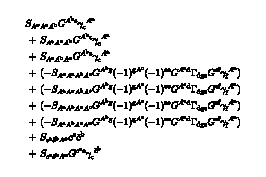

```mathematica
(MakeDSE[A[x]])//.A[_]:>0//FPrint
```

```mathematica
assoc={<|a->b|>}
assoc[[1,Key[a]]]+=4
assoc
```

{<|a→b|>}

4+b

{<|a→4+b|>}

```mathematica
RouteIndices::undeterminedFields="Cannot route indices in expressions with undetermined fields.";
RouteIndices::momentaFailed="Cannot route momenta in the given expression.";

RouteIndices[setup_,expr_FTerm]:=Module[
{openIndices,closedIndices,objects,
ret=ReduceIndices[setup,expr],doFields,idx,a,
indPos,assocField,subObj,subMom,subExtMom,
indStruct,externalIndices,externalMomenta,
f,momRepl,A1111111,AA111111,i,mom,loopMomenta
},

(*We first get all closed, open indices and all indexed objects.*)
doFields=Thread[(#[a__]&/@GetAllFields[setup])->(Field[{#},{a}]&/@GetAllFields[setup])];
openIndices=Sort@GetOpenSuperIndices[setup,ret];
closedIndices=GetClosedSuperIndices[setup,ret];
objects=ExtractObjectsWithIndex[setup,ret]//.doFields;

(*If there are any undetermined fields, we cannot route indices.*)
If[MemberQ[objects[[All,1]],AnyField,{1,4}],Message[RouteIndices::undeterminedFields];Abort[]];

(*As a first step, we insert the correct index structures into all superindices and define momentum variables at every single vertex.
We loop over all closed indices.*)
Do[
(*The indexed object we currently modify. There are always two and we simply grab the first.*)
subObj=Select[objects,MemberQ[#,closedIndices[[idx]],Infinity]&][[1]];
(*The position of the current index inside the subObj*)
indPos=FirstPosition[subObj[[2]],closedIndices[[idx]]][[1]];
(*See what kind of field is associated with the index*)
assocField=subObj[[1,indPos]];
(*Grab the index structure of this field from the setup and assign a new momentum variable*)
indStruct=Map[If[MatchQ[#,_Symbol],Unique[SymbolName[#]],#]&,FieldSetupIndices[setup,assocField],{1,3}];
indStruct[[1]]=loopMomentum[indStruct[[1]]];

(*replace all occurences of the superindex with the fitting index structure. 
We want to keep the index sign in the momenta, but remove it from the group indices*)
ret=ret/.closedIndices[[idx]]->indStruct;
ret=ret/.(-indStruct[[2]])->indStruct[[2]];
objects=objects/.closedIndices[[idx]]->indStruct;
objects=objects/.(-indStruct[[2]])->indStruct[[2]];

,{idx,1,Length[closedIndices]}];

(*Next, we treat the external superindices. We assign to each an open group structure and a new momentum p1,p2,... 
Momentum conservation is already enforced here, i.e. ∑_i Subscript[p, i]=0 and we choose Subscript[p, n]=-∑_(i<n) Subscript[p, i] for the last momentum Subscript[p, n].*)
externalIndices=Table[{},{idx,1,Length[openIndices]}];
Do[
(*see above*)
subObj=Select[objects,MemberQ[#,openIndices[[idx]],Infinity]&][[1]];
indPos=FirstPosition[subObj[[2]],openIndices[[idx]]][[1]];
assocField=subObj[[1,indPos]];
indStruct=Map[If[MatchQ[#,_Symbol],Symbol[SymbolName[#]<>ToString[idx]],#]&,FieldSetupIndices[setup,assocField],{1,3}];

(*Subscript[p, n]=-∑_(i<n) Subscript[p, i]*)
If[idx===Length[openIndices],indStruct[[1]]=-Total[Values[externalIndices][[;;idx-1,1]]]];

ret=ret/.openIndices[[idx]]->indStruct;
ret=ret/.(-indStruct)->indStruct;
objects=objects/.openIndices[[idx]]->indStruct;
objects=objects/.(-indStruct)->indStruct;

(*This is information for the user, which we will return.*)
externalIndices[[idx]]=openIndices[[idx]]->indStruct;

,{idx,1,Length[openIndices]}];

(*extract a list of all new external momenta*)
externalMomenta=Values[externalIndices][[All,1]];

(*Now, we do the momentum routing.*)
Do[
subObj=objects[[idx]];
subMom=subObj[[2,All,1]];
(*See if the object has any external (sub-)momenta*)
subExtMom=Select[subMom,(ContainsAny[externalMomenta,makePosIdx/@Flatten[{#/.Plus[a_,b__]:>List[a,b]}]])&];

(*if momentum conservation is already fulfilled, do nothing*)
If[Total@subMom===0,Continue[]];

(*Case 1: we have no external momentum anywhere in the legs of the current object*)
If[Length[subExtMom]===0,
(*for safety, we try to route our momenta through fermions. At 1-loop this is irrelevant, at n-loop it is not.*)
f=FirstPosition[IsFermion[setup,#]&/@subObj[[1]],True][[1]];
If[f==="NotFound",f=1];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

(*Case 2: we have at least one momentum without an external one*)
If[Length[subExtMom]<Length[subMom],
(*for safety, we try to route our momenta through fermions.*)
f=FirstPosition[
Table[
(IsFermion[setup,subObj[[1,i]]]&&ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
(*If no fermions are present, simply grab the index which does not contain external momenta.*)
If[f==="NotFound",
f=FirstPosition[
Table[(ContainsNone[externalMomenta,makePosIdx/@Flatten[{subObj[[2,i,1]]/.Plus[a_,b__]:>List[a,b]}]])
,{i,1,Length[subObj[[1]]]}]
,True][[1]];
];

mom=Select[Flatten[{subObj[[2,f,1]]/.Plus[a_,b__]:>List[a,b]}],(MatchQ[#,loopMomentum[_]]||MatchQ[-#,loopMomentum[_]])&][[1]];
momRepl=If[isNeg[mom],
-mom->-mom+Total[subObj[[2,All,1]]],
mom->mom-Total[subObj[[2,All,1]]]
];

objects=objects/.momRepl;
ret=ret/.momRepl;

Continue[];
];

Abort[];
,{idx,1,Length[objects]}];

(*Sanity check to see that we did not make an error*)
Do[
subObj=objects[[idx]];
If[Total[subObj[[2,All,1]]]=!=0,Message[RouteIndices::momentaFailed];Abort[]];
,{idx,1,Length[objects]}];

(*replace the loopMomenta[...] by l1, l2, ...*)
ClearAll@@Table["l"<>ToString[idx],{idx,1,50}];
loopMomenta=Cases[objects[[All,2,1]],loopMomentum[_],Infinity]//DeleteDuplicates;
ret=ret/.Thread[loopMomenta->Table[Symbol["l"<>ToString[idx]],{idx,1,Length[loopMomenta]}]];
loopMomenta=loopMomenta/.Thread[loopMomenta->Table[Symbol["l"<>ToString[idx]],{idx,1,Length[loopMomenta]}]];


Return[<|
"result"->ret,
"externalIndices"->externalIndices,
"loopMomenta"->loopMomenta
|>];
];

RouteIndices[setup_,expr_FEq]:=Module[{results,ret,idx,subidx},
results=RouteIndices[setup,#]&/@(List@@expr);

(*All terms have the same loop momenta and external legs*)
If[Equal@@Map[#["loopMomenta"]&,results]&&
Equal@@Map[#["externalIndices"]&,results],
Return[<|
"result"->FEq@@Map[#["result"]&,results],
"externalIndices"->results[[1]]["externalIndices"],
"loopMomenta"->results[[1]]["loopMomenta"]
|>]
];

(*All terms have the same external legs, but different loop orders*)
If[Equal@@Map[#["externalIndices"]&,results],
ret={results[[1]]};
Do[
For[subidx=1,subidx<=Length[ret]+1,subidx++,
If[subidx===Length[ret]+1,
AppendTo[ret,results[[idx]]];
Break[];
];
If[ret[[subidx]]["loopMomenta"]===results[[idx]]["loopMomenta"],
ret[[subidx,Key["result"]]]=FEq[ret[[subidx,Key["result"]]],results[[idx]]["result"]];
Break[];
];
];
,{idx,2,Length[results]}];
Return[SortBy[ret,Length[#["loopMomenta"]]&]]
];

(*All terms are different*)
Return[results];
];
(MakeDSE[A[x]]//.A[_]:>0)//Truncate;
RouteIndices[Setup,%]
```

{<|result→FTerm[S[{c,cb,A},{{0,{c10703}},{0,{c10705}},{0,{v1,c1}}}],c[{0,{c10703}}],cb[{0,{c10705}}]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{}|>,<|result→FEq[FTerm[S[{A,A,A},{{0,{v1,c1}},{l1,{v10613,c10614}},{-l1,{v10616,c10617}}}],Propagator[{A,A},{{-l1,{v10613,c10614}},{l1,{v10616,c10617}}}]],FTerm[S[{A,A,A},{{l1,{v10619,c10620}},{0,{v1,c1}},{-l1,{v10622,c10623}}}],Propagator[{A,A},{{-l1,{v10619,c10620}},{l1,{v10622,c10623}}}]],FTerm[S[{A,A,A},{{l1,{v10625,c10626}},{-l1,{v10628,c10629}},{0,{v1,c1}}}],Propagator[{A,A},{{-l1,{v10625,c10626}},{l1,{v10628,c10629}}}]],FTerm[-1,S[{c,cb,A},{{l1,{c10707}},{-l1,{c10709}},{0,{v1,c1}}}],Propagator[{cb,c},{{l1,{c10709}},{-l1,{c10707}}}]]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1}|>,<|result→FEq[FTerm[-1,S[{A,A,A,A},{{0,{v1,c1}},{l2,{v10631,c10632}},{-l1,{v10634,c10635}},{l1-l2,{v10637,c10638}}}],Propagator[{A,A},{{-l1,{v10646,c10647}},{l1,{v10634,c10635}}}],Propagator[{A,A},{{l1-l2,{v10640,c10641}},{-l1+l2,{v10637,c10638}}}],GammaN[{A,A,A},{{-l1+l2,{v10640,c10641}},{l1,{v10646,c10647}},{-l2,{v10643,c10644}}}],Propagator[{A,A},{{-l2,{v10631,c10632}},{l2,{v10643,c10644}}}]],FTerm[-1,S[{A,A,A,A},{{l1,{v10649,c10650}},{0,{v1,c1}},{-l2,{v10652,c10653}},{-l1+l2,{v10655,c10656}}}],Propagator[{A,A},{{-l2,{v10664,c10665}},{l2,{v10652,c10653}}}],Propagator[{A,A},{{-l1+l2,{v10658,c10659}},{l1-l2,{v10655,c10656}}}],GammaN[{A,A,A},{{l1-l2,{v10658,c10659}},{l2,{v10664,c10665}},{-l1,{v10661,c10662}}}],Propagator[{A,A},{{-l1,{v10649,c10650}},{l1,{v10661,c10662}}}]],FTerm[-1,S[{A,A,A,A},{{l1,{v10667,c10668}},{-l2,{v10670,c10671}},{0,{v1,c1}},{-l1+l2,{v10673,c10674}}}],Propagator[{A,A},{{-l2,{v10682,c10683}},{l2,{v10670,c10671}}}],Propagator[{A,A},{{-l1+l2,{v10676,c10677}},{l1-l2,{v10673,c10674}}}],GammaN[{A,A,A},{{l1-l2,{v10676,c10677}},{l2,{v10682,c10683}},{-l1,{v10679,c10680}}}],Propagator[{A,A},{{-l1,{v10667,c10668}},{l1,{v10679,c10680}}}]],FTerm[-1,S[{A,A,A,A},{{l1,{v10685,c10686}},{-l2,{v10688,c10689}},{-l1+l2,{v10691,c10692}},{0,{v1,c1}}}],Propagator[{A,A},{{-l2,{v10700,c10701}},{l2,{v10688,c10689}}}],Propagator[{A,A},{{-l1+l2,{v10694,c10695}},{l1-l2,{v10691,c10692}}}],GammaN[{A,A,A},{{l1-l2,{v10694,c10695}},{l2,{v10700,c10701}},{-l1,{v10697,c10698}}}],Propagator[{A,A},{{-l1,{v10685,c10686}},{l1,{v10697,c10698}}}]]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1,l2}|>}

2 and 1

Association::setps: <|result→FTerm[S[{A,A,A},{{0,{v1,c1}},{l1,{v9533,c9534}},{-l1,{v9536,c9537}}}],Propagator[{A,A},{{-l1,{v9533,c9534}},{l1,{v9536,c9537}}}]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1}|> in the part assignment is not a symbol.

3 and 1

Association::setps: <|result→FTerm[S[{A,A,A},{{0,{v1,c1}},{l1,{v9533,c9534}},{-l1,{v9536,c9537}}}],Propagator[{A,A},{{-l1,{v9533,c9534}},{l1,{v9536,c9537}}}]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1}|> in the part assignment is not a symbol.

4 and 1

4 and 2

{<|result→FTerm[S[{A,A,A},{{0,{v1,c1}},{l1,{v9533,c9534}},{-l1,{v9536,c9537}}}],Propagator[{A,A},{{-l1,{v9533,c9534}},{l1,{v9536,c9537}}}]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1}|>,<|result→FTerm[-1,S[{A,A,A,A},{{0,{v1,c1}},{l2,{v9551,c9552}},{-l1,{v9554,c9555}},{l1-l2,{v9557,c9558}}}],Propagator[{A,A},{{-l1,{v9566,c9567}},{l1,{v9554,c9555}}}],Propagator[{A,A},{{l1-l2,{v9560,c9561}},{-l1+l2,{v9557,c9558}}}],GammaN[{A,A,A},{{-l1+l2,{v9560,c9561}},{l1,{v9566,c9567}},{-l2,{v9563,c9564}}}],Propagator[{A,A},{{-l2,{v9551,c9552}},{l2,{v9563,c9564}}}]],externalIndices→{x→{0,{v1,c1}}},loopMomenta→{l1,l2}|>}

```mathematica
TakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//Truncate;
RouteIndices[Setup,%]
```

<|result→FEq[FTerm[-1/2,Propagator[{cb,c},{{l1,{c8709}},{-l1,{c8713}}}],GammaN[{c,cb,A},{{l1,{c8713}},{-l1-p1,{c8719}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1+p1,{c8719}},{-l1-p1,{c8715}}}],GammaN[{c,cb,A},{{l1+p1,{c8715}},{-l1-p1-p2,{c8721}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1+p1+p2,{c8721}},{-l1-p1-p2,{c8717}}}],GammaN[{c,cb,A},{{l1+p1+p2,{c8717}},{-l1,{c8723}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1,{c8723}},{-l1,{c8711}}}],Rdot[{c,cb},{{l1,{c8711}},{-l1,{c8709}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8729}},{-l1,{c8725}}}],GammaN[{c,cb,A},{{l1-p1,{c8735}},{-l1,{c8729}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p1,{c8731}},{-l1+p1,{c8735}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c8737}},{-l1+p1,{c8731}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1-p1-p2,{c8733}},{-l1+p1+p2,{c8737}}}],GammaN[{c,cb,A},{{l1,{c8739}},{-l1+p1+p2,{c8733}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1,{c8727}},{-l1,{c8739}}}],Rdot[{c,cb},{{l1,{c8725}},{-l1,{c8727}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v8747,c8748}},{l1,{v8741,c8742}}}],GammaN[{A,A,A},{{l1,{v8747,c8748}},{p1,{v1,c1}},{-l1-p1,{v8756,c8757}}}],Propagator[{A,A},{{-l1-p1,{v8750,c8751}},{l1+p1,{v8756,c8757}}}],GammaN[{A,A,A},{{l1+p1,{v8750,c8751}},{p2,{v2,c2}},{-l1-p1-p2,{v8759,c8760}}}],Propagator[{A,A},{{-l1-p1-p2,{v8753,c8754}},{l1+p1+p2,{v8759,c8760}}}],GammaN[{A,A,A},{{l1+p1+p2,{v8753,c8754}},{-p1-p2,{v3,c3}},{-l1,{v8762,c8763}}}],Propagator[{A,A},{{-l1,{v8744,c8745}},{l1,{v8762,c8763}}}],Rdot[{A,A},{{-l1,{v8741,c8742}},{l1,{v8744,c8745}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v8771,c8772}},{l1,{v8765,c8766}}}],GammaN[{A,A,A,A},{{p1,{v1,c1}},{l1,{v8771,c8772}},{p2,{v2,c2}},{-l1-p1-p2,{v8777,c8778}}}],Propagator[{A,A},{{-l1-p1-p2,{v8774,c8775}},{l1+p1+p2,{v8777,c8778}}}],GammaN[{A,A,A},{{l1+p1+p2,{v8774,c8775}},{-p1-p2,{v3,c3}},{-l1,{v8780,c8781}}}],Propagator[{A,A},{{-l1,{v8768,c8769}},{l1,{v8780,c8781}}}],Rdot[{A,A},{{-l1,{v8765,c8766}},{l1,{v8768,c8769}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8783}},{-l1,{c8789}}}],GammaN[{c,cb,A},{{l1,{c8789}},{-l1-p2,{c8795}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1+p2,{c8795}},{-l1-p2,{c8787}}}],GammaN[{c,cb,A},{{l1+p2,{c8787}},{-l1-p1-p2,{c8793}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1+p1+p2,{c8793}},{-l1-p1-p2,{c8791}}}],GammaN[{c,cb,A},{{l1+p1+p2,{c8791}},{-l1,{c8797}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1,{c8797}},{-l1,{c8785}}}],Rdot[{c,cb},{{l1,{c8785}},{-l1,{c8783}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8805}},{-l1,{c8799}}}],GammaN[{c,cb,A},{{l1-p2,{c8811}},{-l1,{c8805}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1-p2,{c8803}},{-l1+p2,{c8811}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c8809}},{-l1+p2,{c8803}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p1-p2,{c8807}},{-l1+p1+p2,{c8809}}}],GammaN[{c,cb,A},{{l1,{c8813}},{-l1+p1+p2,{c8807}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1,{c8801}},{-l1,{c8813}}}],Rdot[{c,cb},{{l1,{c8799}},{-l1,{c8801}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v8824,c8825}},{l1,{v8815,c8816}}}],GammaN[{A,A,A},{{l1,{v8824,c8825}},{p2,{v2,c2}},{-l1-p2,{v8833,c8834}}}],Propagator[{A,A},{{-l1-p2,{v8821,c8822}},{l1+p2,{v8833,c8834}}}],GammaN[{A,A,A},{{l1+p2,{v8821,c8822}},{p1,{v1,c1}},{-l1-p1-p2,{v8830,c8831}}}],Propagator[{A,A},{{-l1-p1-p2,{v8827,c8828}},{l1+p1+p2,{v8830,c8831}}}],GammaN[{A,A,A},{{l1+p1+p2,{v8827,c8828}},{-p1-p2,{v3,c3}},{-l1,{v8836,c8837}}}],Propagator[{A,A},{{-l1,{v8818,c8819}},{l1,{v8836,c8837}}}],Rdot[{A,A},{{-l1,{v8815,c8816}},{l1,{v8818,c8819}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v8845,c8846}},{l1,{v8839,c8840}}}],GammaN[{A,A,A},{{l1,{v8845,c8846}},{p2,{v2,c2}},{-l1-p2,{v8851,c8852}}}],Propagator[{A,A},{{-l1-p2,{v8848,c8849}},{l1+p2,{v8851,c8852}}}],GammaN[{A,A,A,A},{{p1,{v1,c1}},{l1+p2,{v8848,c8849}},{-p1-p2,{v3,c3}},{-l1,{v8854,c8855}}}],Propagator[{A,A},{{-l1,{v8842,c8843}},{l1,{v8854,c8855}}}],Rdot[{A,A},{{-l1,{v8839,c8840}},{l1,{v8842,c8843}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8857}},{-l1,{c8863}}}],GammaN[{c,cb,A},{{l1,{c8863}},{-l1-p2,{c8869}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1+p2,{c8869}},{-l1-p2,{c8865}}}],GammaN[{c,cb,A},{{l1+p2,{c8865}},{-l1+p1,{c8871}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1-p1,{c8871}},{-l1+p1,{c8861}}}],GammaN[{c,cb,A},{{l1-p1,{c8861}},{-l1,{c8867}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1,{c8867}},{-l1,{c8859}}}],Rdot[{c,cb},{{l1,{c8859}},{-l1,{c8857}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8879}},{-l1,{c8873}}}],GammaN[{c,cb,A},{{l1-p2,{c8885}},{-l1,{c8879}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1-p2,{c8881}},{-l1+p2,{c8885}}}],GammaN[{c,cb,A},{{l1+p1,{c8887}},{-l1+p2,{c8881}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1+p1,{c8877}},{-l1-p1,{c8887}}}],GammaN[{c,cb,A},{{l1,{c8883}},{-l1-p1,{c8877}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1,{c8875}},{-l1,{c8883}}}],Rdot[{c,cb},{{l1,{c8873}},{-l1,{c8875}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v8898,c8899}},{l1,{v8889,c8890}}}],GammaN[{A,A,A},{{l1,{v8898,c8899}},{p2,{v2,c2}},{-l1-p2,{v8907,c8908}}}],Propagator[{A,A},{{-l1-p2,{v8901,c8902}},{l1+p2,{v8907,c8908}}}],GammaN[{A,A,A},{{l1+p2,{v8901,c8902}},{-p1-p2,{v3,c3}},{-l1+p1,{v8910,c8911}}}],Propagator[{A,A},{{-l1+p1,{v8895,c8896}},{l1-p1,{v8910,c8911}}}],GammaN[{A,A,A},{{l1-p1,{v8895,c8896}},{p1,{v1,c1}},{-l1,{v8904,c8905}}}],Propagator[{A,A},{{-l1,{v8892,c8893}},{l1,{v8904,c8905}}}],Rdot[{A,A},{{-l1,{v8889,c8890}},{l1,{v8892,c8893}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v8919,c8920}},{l1,{v8913,c8914}}}],GammaN[{A,A,A},{{l1,{v8919,c8920}},{p1,{v1,c1}},{-l1-p1,{v8925,c8926}}}],Propagator[{A,A},{{-l1-p1,{v8922,c8923}},{l1+p1,{v8925,c8926}}}],GammaN[{A,A,A,A},{{p2,{v2,c2}},{l1+p1,{v8922,c8923}},{-p1-p2,{v3,c3}},{-l1,{v8928,c8929}}}],Propagator[{A,A},{{-l1,{v8916,c8917}},{l1,{v8928,c8929}}}],Rdot[{A,A},{{-l1,{v8913,c8914}},{l1,{v8916,c8917}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v8940,c8941}},{l1,{v8931,c8932}}}],GammaN[{A,A,A,A},{{p2,{v2,c2}},{l1,{v8940,c8941}},{-p1-p2,{v3,c3}},{-l1+p1,{v8946,c8947}}}],Propagator[{A,A},{{-l1+p1,{v8937,c8938}},{l1-p1,{v8946,c8947}}}],GammaN[{A,A,A},{{l1-p1,{v8937,c8938}},{p1,{v1,c1}},{-l1,{v8943,c8944}}}],Propagator[{A,A},{{-l1,{v8934,c8935}},{l1,{v8943,c8944}}}],Rdot[{A,A},{{-l1,{v8931,c8932}},{l1,{v8934,c8935}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8949}},{-l1,{c8953}}}],GammaN[{c,cb,A},{{l1,{c8953}},{-l1-p1,{c8959}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1+p1,{c8959}},{-l1-p1,{c8957}}}],GammaN[{c,cb,A},{{l1+p1,{c8957}},{-l1+p2,{c8963}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1-p2,{c8963}},{-l1+p2,{c8955}}}],GammaN[{c,cb,A},{{l1-p2,{c8955}},{-l1,{c8961}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1,{c8961}},{-l1,{c8951}}}],Rdot[{c,cb},{{l1,{c8951}},{-l1,{c8949}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c8969}},{-l1,{c8965}}}],GammaN[{c,cb,A},{{l1-p1,{c8975}},{-l1,{c8969}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p1,{c8973}},{-l1+p1,{c8975}}}],GammaN[{c,cb,A},{{l1+p2,{c8979}},{-l1+p1,{c8973}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1+p2,{c8971}},{-l1-p2,{c8979}}}],GammaN[{c,cb,A},{{l1,{c8977}},{-l1-p2,{c8971}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1,{c8967}},{-l1,{c8977}}}],Rdot[{c,cb},{{l1,{c8965}},{-l1,{c8967}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v8987,c8988}},{l1,{v8981,c8982}}}],GammaN[{A,A,A},{{l1,{v8987,c8988}},{p1,{v1,c1}},{-l1-p1,{v8996,c8997}}}],Propagator[{A,A},{{-l1-p1,{v8993,c8994}},{l1+p1,{v8996,c8997}}}],GammaN[{A,A,A},{{l1+p1,{v8993,c8994}},{-p1-p2,{v3,c3}},{-l1+p2,{v9002,c9003}}}],Propagator[{A,A},{{-l1+p2,{v8990,c8991}},{l1-p2,{v9002,c9003}}}],GammaN[{A,A,A},{{l1-p2,{v8990,c8991}},{p2,{v2,c2}},{-l1,{v8999,c9000}}}],Propagator[{A,A},{{-l1,{v8984,c8985}},{l1,{v8999,c9000}}}],Rdot[{A,A},{{-l1,{v8981,c8982}},{l1,{v8984,c8985}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v9014,c9015}},{l1,{v9005,c9006}}}],GammaN[{A,A,A,A},{{p1,{v1,c1}},{l1,{v9014,c9015}},{-p1-p2,{v3,c3}},{-l1+p2,{v9020,c9021}}}],Propagator[{A,A},{{-l1+p2,{v9011,c9012}},{l1-p2,{v9020,c9021}}}],GammaN[{A,A,A},{{l1-p2,{v9011,c9012}},{p2,{v2,c2}},{-l1,{v9017,c9018}}}],Propagator[{A,A},{{-l1,{v9008,c9009}},{l1,{v9017,c9018}}}],Rdot[{A,A},{{-l1,{v9005,c9006}},{l1,{v9008,c9009}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c9023}},{-l1,{c9031}}}],GammaN[{c,cb,A},{{l1,{c9031}},{-l1+p1+p2,{c9037}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1-p1-p2,{c9037}},{-l1+p1+p2,{c9027}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c9027}},{-l1+p2,{c9033}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1-p2,{c9033}},{-l1+p2,{c9029}}}],GammaN[{c,cb,A},{{l1-p2,{c9029}},{-l1,{c9035}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1,{c9035}},{-l1,{c9025}}}],Rdot[{c,cb},{{l1,{c9025}},{-l1,{c9023}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c9047}},{-l1,{c9039}}}],GammaN[{c,cb,A},{{l1+p1+p2,{c9053}},{-l1,{c9047}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1+p1+p2,{c9043}},{-l1-p1-p2,{c9053}}}],GammaN[{c,cb,A},{{l1+p2,{c9049}},{-l1-p1-p2,{c9043}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1+p2,{c9045}},{-l1-p2,{c9049}}}],GammaN[{c,cb,A},{{l1,{c9051}},{-l1-p2,{c9045}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1,{c9041}},{-l1,{c9051}}}],Rdot[{c,cb},{{l1,{c9039}},{-l1,{c9041}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v9067,c9068}},{l1,{v9055,c9056}}}],GammaN[{A,A,A},{{l1,{v9067,c9068}},{-p1-p2,{v3,c3}},{-l1+p1+p2,{v9076,c9077}}}],Propagator[{A,A},{{-l1+p1+p2,{v9061,c9062}},{l1-p1-p2,{v9076,c9077}}}],GammaN[{A,A,A},{{l1-p1-p2,{v9061,c9062}},{p1,{v1,c1}},{-l1+p2,{v9070,c9071}}}],Propagator[{A,A},{{-l1+p2,{v9064,c9065}},{l1-p2,{v9070,c9071}}}],GammaN[{A,A,A},{{l1-p2,{v9064,c9065}},{p2,{v2,c2}},{-l1,{v9073,c9074}}}],Propagator[{A,A},{{-l1,{v9058,c9059}},{l1,{v9073,c9074}}}],Rdot[{A,A},{{-l1,{v9055,c9056}},{l1,{v9058,c9059}}}]],FTerm[1/2,Propagator[{A,A},{{-l1,{v9088,c9089}},{l1,{v9079,c9080}}}],GammaN[{A,A,A},{{l1,{v9088,c9089}},{-p1-p2,{v3,c3}},{-l1+p1+p2,{v9094,c9095}}}],Propagator[{A,A},{{-l1+p1+p2,{v9085,c9086}},{l1-p1-p2,{v9094,c9095}}}],GammaN[{A,A,A,A},{{p1,{v1,c1}},{l1-p1-p2,{v9085,c9086}},{p2,{v2,c2}},{-l1,{v9091,c9092}}}],Propagator[{A,A},{{-l1,{v9082,c9083}},{l1,{v9091,c9092}}}],Rdot[{A,A},{{-l1,{v9079,c9080}},{l1,{v9082,c9083}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c9097}},{-l1,{c9105}}}],GammaN[{c,cb,A},{{l1,{c9105}},{-l1+p1+p2,{c9111}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1-p1-p2,{c9111}},{-l1+p1+p2,{c9103}}}],GammaN[{c,cb,A},{{l1-p1-p2,{c9103}},{-l1+p1,{c9109}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1-p1,{c9109}},{-l1+p1,{c9101}}}],GammaN[{c,cb,A},{{l1-p1,{c9101}},{-l1,{c9107}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1,{c9107}},{-l1,{c9099}}}],Rdot[{c,cb},{{l1,{c9099}},{-l1,{c9097}}}]],FTerm[-1/2,Propagator[{cb,c},{{l1,{c9121}},{-l1,{c9113}}}],GammaN[{c,cb,A},{{l1+p1+p2,{c9127}},{-l1,{c9121}},{-p1-p2,{v3,c3}}}],Propagator[{cb,c},{{l1+p1+p2,{c9119}},{-l1-p1-p2,{c9127}}}],GammaN[{c,cb,A},{{l1+p1,{c9125}},{-l1-p1-p2,{c9119}},{p2,{v2,c2}}}],Propagator[{cb,c},{{l1+p1,{c9117}},{-l1-p1,{c9125}}}],GammaN[{c,cb,A},{{l1,{c9123}},{-l1-p1,{c9117}},{p1,{v1,c1}}}],Propagator[{cb,c},{{l1,{c9115}},{-l1,{c9123}}}],Rdot[{c,cb},{{l1,{c9113}},{-l1,{c9115}}}]],FTerm[-1/2,Propagator[{A,A},{{-l1,{v9141,c9142}},{l1,{v9129,c9130}}}],GammaN[{A,A,A},{{l1,{v9141,c9142}},{-p1-p2,{v3,c3}},{-l1+p1+p2,{v9150,c9151}}}],Propagator[{A,A},{{-l1+p1+p2,{v9138,c9139}},{l1-p1-p2,{v9150,c9151}}}],GammaN[{A,A,A},{{l1-p1-p2,{v9138,c9139}},{p2,{v2,c2}},{-l1+p1,{v9147,c9148}}}],Propagator[{A,A},{{-l1+p1,{v9135,c9136}},{l1-p1,{v9147,c9148}}}],GammaN[{A,A,A},{{l1-p1,{v9135,c9136}},{p1,{v1,c1}},{-l1,{v9144,c9145}}}],Propagator[{A,A},{{-l1,{v9132,c9133}},{l1,{v9144,c9145}}}],Rdot[{A,A},{{-l1,{v9129,c9130}},{l1,{v9132,c9133}}}]]],externalIndices→{i1→{p1,{v1,c1}},i2→{p2,{v2,c2}},i3→{-p1-p2,{v3,c3}}},loopMomenta→{l1}|>

## Identification of expressions

```mathematica
StartPoints[setup_,t1_FTerm,t2_FTerm]:=Module[
{obj1,obj2,count,
desired,sList,
match1,match2},
obj1=Sort@Select[ExtractObjectsWithIndex[setup,t1],MemberQ[$indexedObjects,Head@#]&];
obj2=Sort@Select[ExtractObjectsWithIndex[setup,t2],MemberQ[$indexedObjects,Head@#]&];
If[Map[Head[#][#[[1]]]&,obj1]=!=Map[Head[#][#[[1]]]&,obj2],Return[{False,Null}]];
sList=Map[Head[#][#[[1]]]&,obj1];
count=Counts[sList];
desired=Keys[count][[PositionSmallest[Values[count]][[-1]]]];
match1=Select[obj1,(Head[#][#[[1]]]===desired)&][[1]];
match2=Select[obj1,(Head[#][#[[1]]]===desired)&][[1]];
Return[{True,{obj1[[#]],obj2[[#]]}&@PositionSmallest[count]}]
]

test1=TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
test2=TakeDerivatives[WetterichEquation,{A[i1]}]//Truncate;
StartPoints[Setup,test1[[1]],test2[[1]]**FTerm[Propagator[{A,A},{x,y}]]]
StartPoints[Setup,test1[[1]],test2[[1]]]
```

{False,Null}

Rdot[{c,cb}]

{True,{{GammaN[{c,cb,A},{-ic$839,-id$840,-i1}],Propagator[{cb,c},{id$840,b$838}]},{GammaN[{c,cb,A},{-ic$857,-id$858,-i1}],Propagator[{cb,c},{id$858,b$856}]}}}

```mathematica
WetterichEquation//FPrint
```

-Graphics-

```mathematica
(MakeDSE[A[x]]//.A[_]:>0)[[4]]//Truncate;
%//FPrint
RouteIndices[Setup,%%][[1]]
prettyExplicitIndices[Setup,%]
```

-Graphics-

FEq[FTerm[-1,S[{A,A,A,A},{{0,{v1,c1}},{loopMomentum[p557],{v546,c547}},{-loopMomentum[p548],{v549,c550}},{loopMomentum[p548]-loopMomentum[p557],{v552,c553}}}],Propagator[{A,A},{{-loopMomentum[p548],{v561,c562}},{loopMomentum[p548],{v549,c550}}}],Propagator[{A,A},{{loopMomentum[p548]-loopMomentum[p557],{v555,c556}},{-loopMomentum[p548]+loopMomentum[p557],{v552,c553}}}],GammaN[{A,A,A},{{-loopMomentum[p548]+loopMomentum[p557],{v555,c556}},{loopMomentum[p548],{v561,c562}},{-loopMomentum[p557],{v558,c559}}}],Propagator[{A,A},{{-loopMomentum[p557],{v546,c547}},{loopMomentum[p557],{v558,c559}}}]]]

FEq[{{v1,c1},{v549,c550},{v561,c562},{v549,c550},{v561,c562},{v552,c553},{v555,c556},{v546,c547},{v558,c559},{v546,c547},{v558,c559},{v552,c553},{v555,c556}}]

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

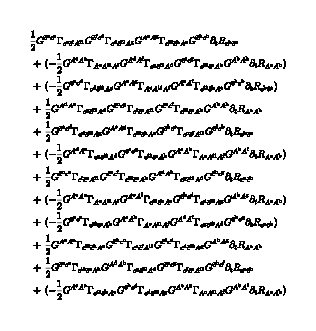

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}]
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
},
S->{
{A,A},{A,A,A},{A,A,A,A},
{cb,c},{cb,c,A}
}
|>;
SetTexStyles[cb->"\\bar{c}"];
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetGlobalSetup[Setup];
DerivativeListAcbc={ A[i1],cb[i2],c[i3]};
TakeDerivatives[Setup,WetterichEquation,DerivativeListAcbc];
%//Truncate//FPrint
```